Function[{σ,b,r},Function[{t,x,y,z},{σ (y-x),r x-y-x z,x y-b z}]]

{0,{20,1,1},1}

{0.0000501999,{19.9905,1.02705,1.00088},0.000347531}

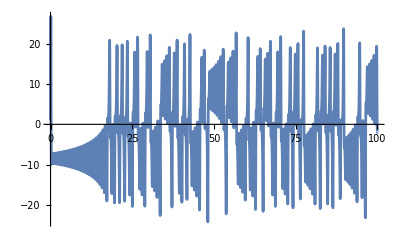

-Graphics3D-

{0,{20,1,1},1}

{(-x+y) σ,r x-y-x z,x y-b z}

{{x→0,y→0,z→0},{x→-√b √(-1+r),y→-√b √(-1+r),z→-1+r},{x→√b √(-1+r),y→√b √(-1+r),z→-1+r}}

(-σ | σ | 0
r-z | -1 | -x
y | x | -b)

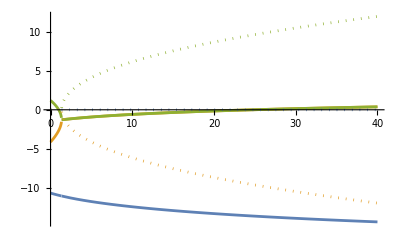

```mathematica
f={σ,b,r}↦{t,x,y,z}↦{
σ(y-x),
r x-y-x z,
x y-b z
}

rkf45=Module[{rkf45prime,β,α,c,cHat,cT},
β=N[{{2/9, 0, 0, 0, 0}, {1/12, 1/4, 0, 0, 0}, {69/128, -243/128, 135/64, 0, 0}, {-17/12, 27/4, -27/5, 16/15, 0}, {65/432, -5/16, 13/16, 4/27, 5/144}}];
α=Total/@β;
c={1/9,0,9/20,16/45,1/12,0};
cHat={47/450,0,12/25,32/225,1/30,6/25};
cT=cHat-c;
rkf45prime={f,tol}↦Apply[{t,x,h}↦Module[
{f0,f1,f2,f3,f4,f5,xNext,xHat,hNext,TE},
f0=f[t,x];
f1=f[t+α⟦1⟧h,x+h(β⟦1,1⟧ f0)];
f2=f[t+α⟦2⟧h,x+h(β⟦2,1⟧ f0+β⟦2,2⟧ f1)];
f3=f[t+α⟦3⟧h,x+h(β⟦3,1⟧ f0+β⟦3,2⟧ f1+β⟦3,3⟧ f2)];
f4=f[t+α⟦4⟧h,x+h(β⟦4,1⟧ f0+β⟦4,2⟧ f1+β⟦4,3⟧ f2+β⟦4,4⟧ f3)];
f5=f[t+α⟦5⟧h,x+h(β⟦5,1⟧ f0+β⟦5,2⟧ f1+β⟦5,3⟧ f2+β⟦5,4⟧ f3+β⟦5,5⟧ f3)];
xNext=x+h(c⟦1⟧f0+c⟦2⟧f1+c⟦3⟧f2+c⟦4⟧f3+c⟦5⟧f4);
xHat=x+h(cHat⟦1⟧f0+cHat⟦2⟧f1+cHat⟦3⟧f2+cHat⟦4⟧f3+cHat⟦5⟧f4+cHat⟦6⟧f5);
TE=h(cT⟦1⟧f0+cT⟦2⟧f1+cT⟦3⟧f2+cT⟦4⟧f3+cT⟦5⟧f4+cT⟦6⟧f5);
hNext=0.9 h(tol/Max[Abs[TE]])^(1/5);
If[
Max[Abs[TE]]>tol,
{t,x,hNext,True},
{t+h,xHat,hNext,False}
]
]];
{f,tol}↦Module[{
stepPrime=rkf45prime[{t,x}↦f[t,Sequence@@x],tol]
},
Apply[{t,x,h}↦Most@NestWhile[stepPrime,{t,x,h,True},#⟦4⟧&]]
]
];



initial={0,{20,1,1},1}
update=rkf45[f[10,8/3,28],10^-6];
update[initial]

data=NestWhileList[update,initial,#[[1]]<100&];

Map[{#[[1]],#[[2,2]]}&,data]//ListLinePlot
lpp=Map[#[[2]]&,data]//ListLinePlot3D[#,BoxRatios->{1, 1, 1},PlotRange->{{-30,30},{-30,30},{0,60}},PlotStyle->{Thin}]&
state=initial
(*Dynamic@Show[lpp,Graphics3D[{Red,Sphere[state[[2]],0.75]}],ImageSize->Large]
While[True,state=update[state];Pause[0.0005]]

{
σ(y-x),
r x-y-x z,
x y-b z
}
Solve[Map[#==0&,%],{x,y,z}]
Grad[%%,{x,y,z}];
%//MatrixForm
%%/.%%%[[1]]//Eigenvalues
%/.r->1//FullSimplify//PowerExpand*)

{
σ(y-x),
r x-y-x z,
x y-b z
}
Solve[Map[#==0&,%],{x,y,z}]
Grad[%%,{x,y,z}];
%//MatrixForm
ReImPlot[Evaluate[%%/.%%%[[2]]/.{σ->10.,b->8./3}//Eigenvalues],{r,0,40}]
```